```mathematica
p={{0},{1},{0}};
```

```mathematica
c={{a},{b}};
```

```mathematica
{a,b}={1.,0.};
```

```mathematica
KroneckerProduct[p,c]//MatrixForm
```

(0
0
a
b
0
0)

```mathematica
KroneckerProduct[c,p]//MatrixForm
```

(0
a
0
0
b
0)

## Operadores

```mathematica
coinA=KroneckerProduct[{{Cos[θA/2],-Sin[θA/2]},{Sin[θA/2],Cos[θA/2]}},baseP];
```

```mathematica
ShiftSparse[t_]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1.,{#,#}]&[2*(2*t+1)]
```

```mathematica
CoinSparse[t_]:=KroneckerProduct[SparseArray[Table[{i,i}->1.,{i,2 t+1}]],SparseArray[FourierMatrix[2]]]
```

```mathematica
USparse[t_]:=ShiftSparse[t].CoinSparse[t]
```

```mathematica
ρ=ArrayPad[Outer[Times,#,Conjugate[#]]&[{a,b}],2];(*vector de estado inicial*)
AbsoluteTiming[Do[ρ=ArrayPad[Chop[#.ρ.ConjugateTranspose[#]]&[U[t]],2],{t,200}]](*hacer los pasos de la DTQW*)
```

{46.9356,Null}

```mathematica
Outer[Times,#,Conjugate[#]]&[{a,b}]//MatrixForm
```

(1. | 0.
0. | 0.)

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

```mathematica
U[1].psi
```

{0.,0.+0.707107 a-0.707107 b,0.,0.,0.+0.707107 a+0.707107 b,0.}

```mathematica
psi=ArrayPad[{a,b},2]
AbsoluteTiming[Do[psi=ArrayPad[Chop[USparse[t].psi],2],{t,250}];]
```

{0,0,1.,0.,0,0}

{0.73539,Null}

```mathematica
{1,2,3}.{1,2,3}†
```

14

```mathematica
{{1,2,3}}ᵀ.Conjugate[{{1,2,3}}]
```

{{1,2,3},{2,4,6},{3,6,9}}

```mathematica
{{1,2,3}}//Conjugate
```

{{1,2,3}}

```mathematica
{{1,2,3}}ᵀ
```

{{1},{2},{3}}

```mathematica
{{1},{2},{3}}.{{1},{2},{3}}†
```

{{1,2,3},{2,4,6},{3,6,9}}

```mathematica
Outer[Times,{1,2,3},{1,2,3}]
```

{{1,2,3},{2,4,6},{3,6,9}}

```mathematica
List/@{1,2,3}
```

{{1},{2},{3}}

```mathematica
(List/@{1,2,3}).(List/@{1,2,3})†
```

{{1,2,3},{2,4,6},{3,6,9}}

```mathematica
List/@psi;
```

```mathematica
Dimensions[List/@psi]
```

{406,1}

```mathematica
Dimensions[(List/@psi)†]
```

{1,406}

```mathematica
Dimensions[#.#†&@(List/@psi)]
```

{406,406}

```mathematica
p=Abs@Diagonal@MatrixPartialTrace[#ᵀ.Conjugate[#]&[{psi}],2,{503,2}];
```

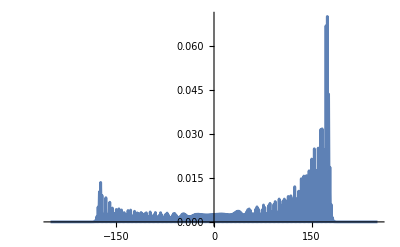

```mathematica
ListPlot[Transpose[{Range[-(250+1),250+1],p}],
Joined->True,
PlotRange->Full]
```

```mathematica
RepeatedTiming[{psi}ᵀ.Conjugate[{psi}];]
```

{0.00690226,Null}

```mathematica
RepeatedTiming[Outer[Times,psi,psi];]
```

{0.493329,Null}